```mathematica
aa[t_,a_,b_]:=Cos[t]a-Sin[t]b
```

```mathematica
bb[t_,a_,b_]:=Sin[t]a+Cos[t]b
```

```mathematica
aa11=RandomReal[{-1,1}]
```

0.0454636

```mathematica
aa12=RandomReal[{-1,1}]
```

-0.632391

```mathematica
aa13=RandomReal[{-1,1}]
```

-0.33737

```mathematica
{aa11,aa12,aa13}
```

{0.0454636,-0.632391,-0.33737}

```mathematica
a11:=Simplify[aa11/Sqrt[aa11^2+aa12^2+aa13^2]]
```

```mathematica
a12:=Simplify[aa12/Sqrt[aa11^2+aa12^2+aa13^2]]
```

```mathematica
a13:=Simplify[aa13/Sqrt[aa11^2+aa12^2+aa13^2]]
```

```mathematica
{a11,a12,a13}
```

{0.0633026,-0.880529,-0.469747}

```mathematica
Simplify[a11^2+a12^2+a13^2]
```

1.

```mathematica
aa21=RandomReal[{-1,1}]
```

0.392303

```mathematica
aa22=RandomReal[{-1,1}]
```

0.809718

```mathematica
aa23 =-(a11 aa21+a12 aa22)/a13
```

-1.46493

```mathematica
{aa21,aa22,aa23}
```

{0.392303,0.809718,-1.46493}

```mathematica
a21:=Simplify[aa21/Sqrt[aa21^2+aa22^2+aa23^2]]
```

```mathematica
a22:=Simplify[aa22/Sqrt[aa21^2+aa22^2+aa23^2]]
```

```mathematica
a23:=Simplify[aa23/Sqrt[aa21^2+aa22^2+aa23^2]]
```

```mathematica
{a21,a22,a23}
```

{0.228193,0.470992,-0.852112}

```mathematica
Simplify[a21^2+a22^2+a23^2]
```

1.

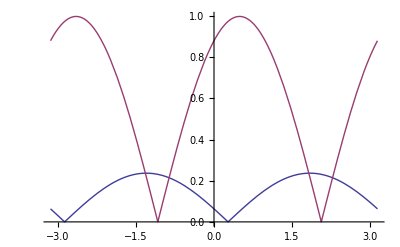

```mathematica
Plot[{Abs[aa[t,a11,a21]],Abs[aa[t,a12,a22]]},{t,-Pi,Pi}]
```

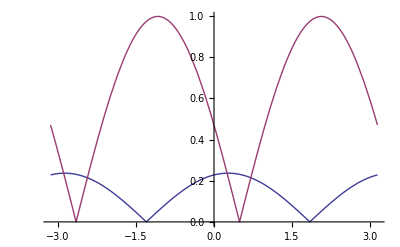

```mathematica
Plot[{Abs[bb[t,a11,a21]],Abs[bb[t,a12,a22]]},{t,-Pi,Pi}]
```

```mathematica
l1[t_,a_,b_,c_,d_]:=Abs[aa[t,a,c]]+Abs[aa[t,b,d]]
```

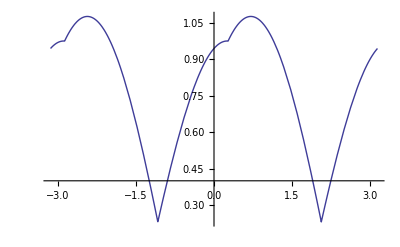

```mathematica
Plot[l1[t,a11,a12,a21,a22],{t,-Pi,Pi}]
```

```mathematica
l2[t_,a_,b_,c_,d_]:=Abs[bb[t,a,c]]+Abs[bb[t,b,d]]
```

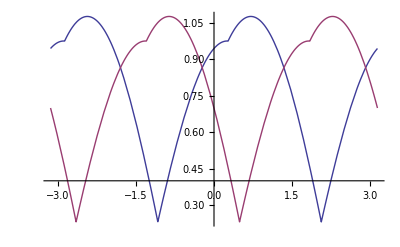

```mathematica
Plot[{l1[t,a11,a12,a21,a22],l2[t,a11,a12,a21,a22]},{t,-Pi,Pi}]
```

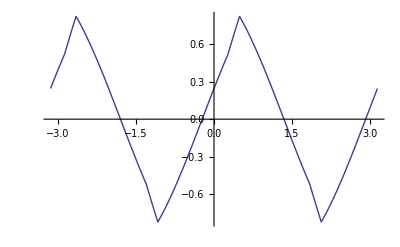

```mathematica
Plot[{l1[t,a11,a12,a21,a22]-l2[t,a11,a12,a21,a22]},{t,-Pi,Pi}]
```

```mathematica
ParametricPlot3D[{aa[t,a11,a21],aa[t,a12,a22],aa[t,a13,a23]},{t,-Pi,Pi},PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

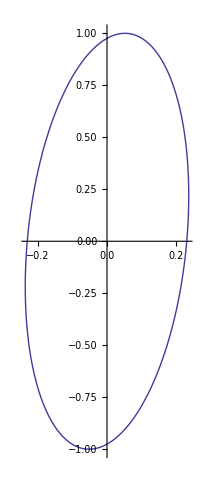

```mathematica
ParametricPlot[{aa[t,a11,a21],aa[t,a12,a22]},{t,-Pi,Pi}]
```

```mathematica
Animate[Show[Graphics3D[{Thick,Red,Arrow[{{0.0,0.0,0.0},{aa[t,a11,a21],aa[t,a12,a22],aa[t,a13,a23]}}]},AspectRatio->1,PlotRange->{{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}}],Graphics3D[{Thick,Red,Arrow[{{0.0,0.0,0.0},{bb[t,a11,a21],bb[t,a12,a22],bb[t,a13,a23]}}]},AspectRatio->1,PlotRange->{{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}}],ParametricPlot3D[{aa[s,a11,a21],aa[s,a12,a22],aa[s,a13,a23]},{s,-Pi,Pi},AspectRatio->1,PlotRange->{{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}},PlotStyle->Directive[Purple,Thick]]],{t,-Pi,Pi},AnimationRunning->False]
```

```mathematica
Diamond1[t_,a11_,a12_,a21_,a22_]:=Line[{{l1[t,a11,a12,a21,a22],0},{0,l1[t,a11,a12,a21,a22]},{-l1[t,a11,a12,a21,a22],0},{0,-l1[t,a11,a12,a21,a22]},{l1[t,a11,a12,a21,a22],0}}]
```

```mathematica
Diamond2[t_,a11_,a12_,a21_,a22_]:=Line[{{l2[t,a11,a12,a21,a22],0},{0,l2[t,a11,a12,a21,a22]},{-l2[t,a11,a12,a21,a22],0},{0,-l2[t,a11,a12,a21,a22]},{l2[t,a11,a12,a21,a22],0}}]
```

```mathematica
Animate[Show[Graphics[{Thick,RGBColor[0,0.6,0],Line[{{1.45,0.0},{1.45,l1[t,a11,a12,a21,a22]-l2[t,a11,a12,a21,a22]}}]},AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],Graphics[{Thick,RGBColor[0.7,0,0.7],Arrow[{{0.0,0.0},{aa[t,a11,a21],aa[t,a12,a22]}}]},AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],Graphics[{Thick,RGBColor[0,0.7,0.7],Arrow[{{0.0,0.0},{bb[t,a11,a21],bb[t,a12,a22]}}]},AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ParametricPlot[{aa[s,a11,a21],aa[s,a12,a22]},{s,-Pi,Pi},AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->Thick],Graphics[{Thick,Gray,Diamond1[t,a11,a12,a21,a22]}],Graphics[{Thick,Gray,Diamond2[t,a11,a12,a21,a22]}]],{t,0,2Pi},AnimationRunning->False]
```

```mathematica
FindAngle[a_,r1_,r2_]:= Module[{aa11,aa12,aa13,a11,a12,a13,aa21,aa22,aa23,a21,a22,a23,n},
aa11=a[[r1,1]];
aa12=a[[r1,2]];
aa13=a[[r1,3]];
a11=Simplify[aa11/Sqrt[aa11^2+aa12^2+aa13^2]];
a12=Simplify[aa12/Sqrt[aa11^2+aa12^2+aa13^2]];
a13=Simplify[aa13/Sqrt[aa11^2+aa12^2+aa13^2]];
aa21=a[[r2,1]];
aa22=a[[r2,2]];
aa23 =a[[r2,3]];
a21=Simplify[aa21/Sqrt[aa21^2+aa22^2+aa23^2]];
a22=Simplify[aa22/Sqrt[aa21^2+aa22^2+aa23^2]];
a23=Simplify[aa23/Sqrt[aa21^2+aa22^2+aa23^2]];
n =FindRoot[l1[t,a11,a12,a21,a22]==l2[t,a11,a12,a21,a22],{t,0}];
n]
```

```mathematica
RotateRows[a_,r1_,r2_,n_]:=Module[{aa11,aa12,aa13,a11,a12,a13,aa21,aa22,aa23,a21,a22,a23,b},
aa11=a[[r1,1]];
aa12=a[[r1,2]];
aa13=a[[r1,3]];
a11=Simplify[aa11/Sqrt[aa11^2+aa12^2+aa13^2]];
a12=Simplify[aa12/Sqrt[aa11^2+aa12^2+aa13^2]];
a13=Simplify[aa13/Sqrt[aa11^2+aa12^2+aa13^2]];
aa21=a[[r2,1]];
aa22=a[[r2,2]];
aa23 =a[[r2,3]];
a21=Simplify[aa21/Sqrt[aa21^2+aa22^2+aa23^2]];
a22=Simplify[aa22/Sqrt[aa21^2+aa22^2+aa23^2]];
a23=Simplify[aa23/Sqrt[aa21^2+aa22^2+aa23^2]];
b=a;
b[[r1,1]]=Cos[t]a11-Sin[t]a21/.n[[1]];
b[[r1,2]]=Cos[t]a12-Sin[t]a22/.n[[1]];
b[[r1,3]]=Cos[t]a13-Sin[t]a23/.n[[1]];
b[[r2,1]]=Sin[t]a11+Cos[t]a21/.n[[1]];
b[[r2,2]]=Sin[t]a12+Cos[t]a22/.n[[1]];
b[[r2,3]]=Sin[t]a13+Cos[t]a23/.n[[1]];
b
]
```

```mathematica
RowSums[a_]:={Abs[a[[1,1]]]+Abs[a[[1,2]]],Abs[a[[2,1]]]+Abs[a[[2,2]]],Abs[a[[3,1]]]+Abs[a[[3,2]]]}
```

```mathematica
MaxSum[a_]:=FullForm[Max[RowSums[a]]]
```

```mathematica
EqualSums[a_]:=Module[{b},
b=a;
sums=RowSums[b];
nmax=Position[sums,Max[sums]][[1]];
nmin=Position[sums,Min[sums]][[1]];
loopnum=0;
loopmax=100;
While[nmax≠nmin&&loopnum<loopmax,
n=FindAngle[b,nmax,nmin];
b=RotateRows[b,nmax,nmin,n];
sums=RowSums[b];
nmax=Position[sums,Max[sums]][[1]];
nmin=Position[sums,Min[sums]][[1]];
loopnum++;
];
b
]
```

```mathematica
a = {{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
b=EqualSums[a]
```

{{0.926763,0.0406712,-0.373439},{-0.304732,0.662702,-0.684079},{0.219656,0.747778,0.626561}}

```mathematica
RowSums[b]
```

{0.967434,0.967434,0.967434}

```mathematica
N[Sqrt[8/9]]
```

0.942809

```mathematica
mina=Simplify[{{Sqrt[2]/2,Sqrt[8/9]-Sqrt[2]/2,2/3},{-Sqrt[2]/2,Sqrt[8/9]-Sqrt[2]/2,2/3},{0,Sqrt[8/9],-1/3}}]
```

{{1/(√2),1/(3 √2),2/3},{-1/(√2),1/(3 √2),2/3},{0,(2 √2)/3,-1/3}}

```mathematica
MatrixForm[mina]
```

(1/(√2) | 1/(3 √2) | 2/3
-1/(√2) | 1/(3 √2) | 2/3
0 | (2 √2)/3 | -1/3)

```mathematica
MatrixForm[mina.Transpose[mina]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
RowSums[mina]
```

{(2 √2)/3,(2 √2)/3,(2 √2)/3}

```mathematica
a0={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[a0]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
rr1[t1_]:={{Cos[t1],-Sin[t1],0},{Sin[t1],Cos[t1],0},{0,0,1}}
```

```mathematica
MatrixForm[rr1[t1]]
```

(Cos[t1] | -Sin[t1] | 0
Sin[t1] | Cos[t1] | 0
0 | 0 | 1)

```mathematica
a1[t1_]:=a0.rr1[t1]
```

```mathematica
MatrixForm[a1[t1]]
```

(Cos[t1] | -Sin[t1] | 0
Sin[t1] | Cos[t1] | 0
0 | 0 | 1)

```mathematica
rr2[t2_]:={{1,0,0},{0,Cos[t2],-Sin[t2]},{0,Sin[t2],Cos[t2]}}
```

```mathematica
MatrixForm[rr2[t2]]
```

(1 | 0 | 0
0 | Cos[t2] | -Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
a2[t1_,t2_]:=a1[t1].rr2[t2]
```

```mathematica
MatrixForm[a2[t1,t2]]
```

(Cos[t1] | -Cos[t2] Sin[t1] | Sin[t1] Sin[t2]
Sin[t1] | Cos[t1] Cos[t2] | -Cos[t1] Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
rr3[t3_]:={{Cos[t3],0,Sin[t3]},{0,1,0},{-Sin[t3],0,Cos[t3]}}
```

```mathematica
MatrixForm[rr3[t3]]
```

(Cos[t3] | 0 | Sin[t3]
0 | 1 | 0
-Sin[t3] | 0 | Cos[t3])

```mathematica
a3[t1_,t2_,t3_]:=a2[t1,t2].rr3[t3]
```

```mathematica
MatrixForm[a3[t1,t2,t3]]
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
c=b
```

{{0.926763,0.0406712,-0.373439},{-0.304732,0.662702,-0.684079},{0.219656,0.747778,0.626561}}

```mathematica
MaxSum[c]
```

0.967434

```mathematica
ct1n=EqualSums[c.a3[-Pi/100,0,0]];MaxSum[ct1n]
```

0.97354

```mathematica
ct1p=EqualSums[c.a3[Pi/100,0,0]];MaxSum[ct1p]
```

0.963767

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/100,0]];MaxSum[ct2n]
```

0.972258

```mathematica
ct2p=EqualSums[c.a3[0,Pi/100,0]];MaxSum[ct2p]
```

0.961075

```mathematica
c=ct2p
```

{{0.931773,0.0293015,-0.361856},{-0.285172,0.675903,-0.679583},{0.224667,0.736408,0.638144}}

```mathematica
MaxSum[c]
```

0.961075

```mathematica
ct1n=EqualSums[c.a3[-Pi/100,0,0]];MaxSum[ct1n]
```

0.967919

```mathematica
ct1p=EqualSums[c.a3[Pi/100,0,0]];MaxSum[ct1p]
```

0.957788

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/100,0]];MaxSum[ct2n]
```

0.968468

```mathematica
ct2p=EqualSums[c.a3[0,Pi/100,0]];MaxSum[ct2p]
```

0.942817

```mathematica
c=ct2p
```

{{0.942805,-0.0000118462,-0.333345},{-0.235698,0.707119,-0.666655},{0.235722,0.707095,0.666672}}

```mathematica
MaxSum[c]
```

0.942817

```mathematica
cinc=50000;
```

```mathematica
ct1n=EqualSums[c.a3[-Pi/cinc,0,0]];MaxSum[ct1n]
```

0.942811

```mathematica
ct1p=EqualSums[c.a3[Pi/cinc,0,0]];MaxSum[ct1p]
```

0.942827

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/cinc,0]];MaxSum[ct2n]
```

0.942811

```mathematica
ct2p=EqualSums[c.a3[0,Pi/cinc,0]];MaxSum[ct2p]
```

0.942839

```mathematica
MatrixForm[c=ct1n]
```

(0.942808 | 3.1437×10^-6 | -0.333336
-0.235707 | 0.707104 | -0.666668
0.235701 | 0.70711 | 0.666664)

```mathematica
MaxSum[c]
```

0.942811

```mathematica
cinc=50000;
```

```mathematica
ct1n=EqualSums[c.a3[-Pi/cinc,0,0]];MaxSum[ct1n]
```

0.942821

```mathematica
ct1p=EqualSums[c.a3[Pi/cinc,0,0]];MaxSum[ct1p]
```

0.942809

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/cinc,0]];MaxSum[ct2n]
```

0.942827

```mathematica
ct2p=EqualSums[c.a3[0,Pi/cinc,0]];MaxSum[ct2p]
```

0.942818

```mathematica
MatrixForm[c=ct1p]
```

(0.942809 | 6.15266×10^-7 | -0.333334
-0.235703 | 0.707106 | -0.666667
0.235702 | 0.707107 | 0.666666)

```mathematica
MaxSum[c]
```

0.942809

```mathematica
cinc=500000;
```

```mathematica
ct1n=EqualSums[c.a3[-Pi/cinc,0,0]];MaxSum[ct1n]
```

0.94281

```mathematica
ct1p=EqualSums[c.a3[Pi/cinc,0,0]];MaxSum[ct1p]
```

0.942809

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/cinc,0]];MaxSum[ct2n]
```

0.942811

```mathematica
ct2p=EqualSums[c.a3[0,Pi/cinc,0]];MaxSum[ct2p]
```

0.94281

```mathematica
MatrixForm[c=ct1p]
```

(0.942809 | -5.36205×10^-7 | -0.333334
-0.235702 | 0.707107 | -0.666666
0.235703 | 0.707106 | 0.666667)

```mathematica
MaxSum[c]
```

0.942809

```mathematica
cinc=500000;
```

```mathematica
ct1n=EqualSums[c.a3[-Pi/cinc,0,0]];MaxSum[ct1n]
```

0.942809

```mathematica
ct1p=EqualSums[c.a3[Pi/cinc,0,0]];MaxSum[ct1p]
```

0.94281

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/cinc,0]];MaxSum[ct2n]
```

0.94281

```mathematica
ct2p=EqualSums[c.a3[0,Pi/cinc,0]];MaxSum[ct2p]
```

0.942811

```mathematica
MatrixForm[c=ct1n]
```

(0.942809 | 3.8368×10^-7 | -0.333334
-0.235703 | 0.707106 | -0.666667
0.235702 | 0.707107 | 0.666666)

```mathematica
MaxSum[c]
```

0.942809

```mathematica
cinc=500000;
```

```mathematica
ct1n=EqualSums[c.a3[-Pi/cinc,0,0]];MaxSum[ct1n]
```

0.94281

```mathematica
ct1p=EqualSums[c.a3[Pi/cinc,0,0]];MaxSum[ct1p]
```

0.942809

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/cinc,0]];MaxSum[ct2n]
```

0.94281

```mathematica
ct2p=EqualSums[c.a3[0,Pi/cinc,0]];MaxSum[ct2p]
```

0.94281

```mathematica
MatrixForm[c=ct1p]
```

(0.942809 | 2.39669×10^-7 | -0.333334
-0.235703 | 0.707107 | -0.666667
0.235702 | 0.707107 | 0.666666)

```mathematica
MaxSum[c]
```

0.942809

```mathematica
cinc=1000000;
```

```mathematica
ct1n=EqualSums[c.a3[-Pi/cinc,0,0]];MaxSum[ct1n]
```

0.94281

```mathematica
ct1p=EqualSums[c.a3[Pi/cinc,0,0]];MaxSum[ct1p]
```

0.942809

```mathematica
ct2n=EqualSums[c.a3[0,-Pi/cinc,0]];MaxSum[ct2n]
```

0.94281

```mathematica
ct2p=EqualSums[c.a3[0,Pi/cinc,0]];MaxSum[ct2p]
```

0.94281

```mathematica
MatrixForm[c=ct1p]
```

(0.942809 | -2.05281×10^-8 | -0.333333
-0.235702 | 0.707107 | -0.666667
0.235702 | 0.707107 | 0.666667)

```mathematica
MaxSum[c]
```

0.942809